```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]


GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]


GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]

BQH[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];


killomega[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}]];
killxi[N1_]:=Join[Table[Subscript[ξ,i]->0,{i,1,N1}]];
killg[N1_]:=Flatten[Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}]];
killchi[N1_]:=Flatten[Table[Subscript[χ,i,j]->0,{i,1,N1},{j,i+1,N1}]];


CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhoton[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonAnal[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+2 d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


QFIperPhotonBQH[Nmodes_,EOM_]:=Module[{DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

QFI limit

2.66667

Mean photon limit

0.5

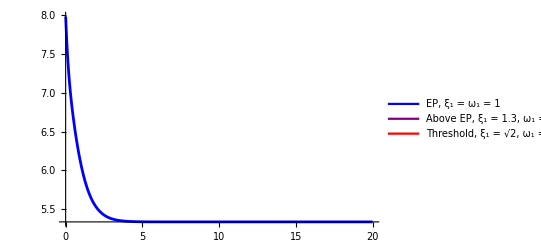

QFI limit

(4-8 ⅇ^(4 t)+ⅇ^(8 t) (4+64 t^2))/((1+ⅇ^(4 t)) (1+2 t) (1+ⅇ^(4 t) (-1+4 t)))

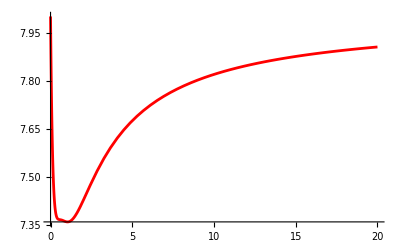

Mean photon limit

2.72581

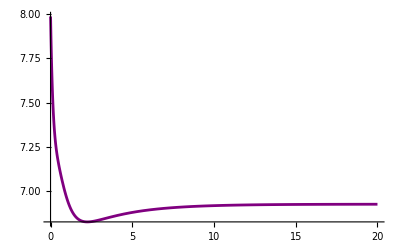

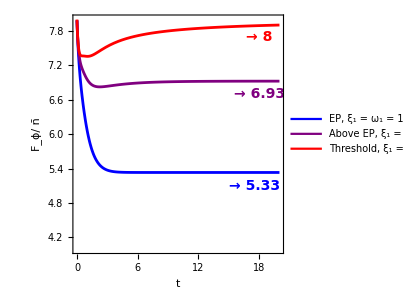

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;
κ=2;

(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=20;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify;
"QFI limit"
Limit[F,t->∞]//N
"Mean photon limit"
Limit[n,t->∞]//N

plt1=Plot[{Evaluate[F/.ϕ->0]/n},{t,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[LineLegend[{Blue,Purple,Red},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.3, ω_1 = 1","Threshold, ξ_1 = √2, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}]]

(* threshold *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=Sqrt[2];
Subscript[ω, 1]=1;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify//Chop;

S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

"QFI limit"
F/n/.ϕ->0//FullSimplify

plt2=Plot[{Evaluate[F/.ϕ->0]/n},{t,0,tmax},PlotRange->All, PlotStyle->Red]


(* above EP *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1.3;
Subscript[ω, 1]=1;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify//Chop;

S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

"Mean photon limit"
Limit[n,t->∞]//N

plt3=Plot[{Evaluate[F/.ϕ->0]/n},{t,0,tmax},PlotRange->All, PlotStyle->Purple]


Show[plt1,plt3,plt2,Frame->True,PlotRange->{4,8},Axes->None,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["t",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ϕ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,Epilog->{Text[Style["→ 6.93",14,Purple,FontFamily->"Arial",Bold],{18,6.7}],Text[Style[TraditionalForm["→ 8"],14,Red,FontFamily->"Arial",Bold],{18,7.7}],Text[Style[" → 5.33",14,Blue,FontFamily->"Arial",Bold],{17.5,5.1}]}]
```

```mathematica
Limit[(4-8 ⅇ^(4 t)+ⅇ^(8 t) (4+64 t^2))/((1+ⅇ^(4 t)) (1+2 t) (1+ⅇ^(4 t) (-1+4 t))),t->∞]
Limit[(4 ⅇ^(-2 √2 t) (9-6 √2-2 ⅇ^(4 √2 t)+(9+6 √2) ⅇ^(8 √2 t)+4 (-4+3 √2) ⅇ^(2 (1+√2) t)+16 ⅇ^(4 (1+√2) t)-4 (4+3 √2) ⅇ^((2+6 √2) t)))/((2-√2+(2+√2) ⅇ^(4 √2 t)-4 ⅇ^(2 (1+√2) t)) (2 Cosh[2 t]-4 Sinh[2 t]+3 √2 Sinh[2 √2 t])),t->∞]//N
Limit[(28+38 Cosh[2 t]+28 Cosh[4 t]+50 Cosh[6 t]+8 Sinh[2 t]+8 Sinh[4 t]+40 Sinh[6 t])/((1+2 Cosh[2 t]+Sinh[2 t]) (6 Cosh[2 t]-4 Sinh[2 t]+5 Sinh[4 t])),t->∞]//N
```

8

9.65685

12.

```mathematica
(*PHASE SPACE*)
```

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;
κ=2;

(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=20;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;


G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];

DensityPlot[1/(2 π Sqrt[Det[Σin]]) Exp[-1/2 {x,p}.Inverse[Σin].{x,p}]/.t->tmax,{x,-10,10},{p,-10,10}]


(* threshold *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=Sqrt[2];
Subscript[ω, 1]=1;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify//Chop;

S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;


G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];

DensityPlot[1/(2 π Sqrt[Det[Σin]]) Exp[-1/2 {x,p}.Inverse[Σin].{x,p}]/.t->tmax,{x,-10,10},{p,-10,10}]

(* above EP *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1.3;
Subscript[ω, 1]=1;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify//Chop;

S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;


G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];

DensityPlot[1/(2 π Sqrt[Det[Σin]]) Exp[-1/2 {x,p}.Inverse[Σin].{x,p}]/.t->tmax,{x,-10,10},{p,-10,10}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* steady-state analytical *)
$Assumptions={Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
"EOM is"
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

"DM is"
DM//FullSimplify//MatrixForm

"DM eigenvalues are"
DM//Eigenvalues//FullSimplify

"Stability threshold is"
Solve[-κ/2+√(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)==0,κ]//FullSimplify[Assuming[{Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals,#]]&

"SS covariance matrix"
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify;
Σin//MatrixForm
"Wigner"
(*1/(2 π Sqrt[Det[Σin]]) Exp[-1/2 {x,p}.Inverse[Σin].{x,p}]//FullSimplify*)
-1/2 {x,p}.Inverse[Σin].{x,p}//FullSimplify
Sqrt[Det[Σin]]//FullSimplify

"Wigner at thresdhol"
1/(2 π Sqrt[Det[Σin]]) Exp[-1/2 {x,p}.Inverse[Σin].{x,p}]/.κ->2 √(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)//FullSimplify


G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
"Purity"
μsq=1/Det[Σout]//FullSimplify

"QFI is"
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify
"QFI at stability"
F/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+κ^2/4]//FullSimplify

"Mean photon number is"
n=1/4 (Tr[Σin]- 2 Nmodes)//FullSimplify
"mean photon at stability"
n/.κ->2 √(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)//FullSimplify

"QFI normalized to mean"
Fn=F/n//FullSimplify
"QFI normalized at stability"
F/n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+κ^2/4]//FullSimplify


"QFI at EP"
F/n/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify
"n at EP"
n/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify

"EP"
F/n/.Subscript[ξ, 1]->1/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N
n/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N


"Above EP"
F/n/.Subscript[ξ, 1]->1.3/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}
n/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}



"At Threshold"
F/n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1//FullSimplify
F/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1
n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1
Eigensystem[DM/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

EOM is

(-κ/2-ⅈ ω_1 | ξ_1
ξ_1 | -κ/2+ⅈ ω_1)

DM is

(-κ/2+ξ_1 | ω_1
-ω_1 | -κ/2-ξ_1)

DM eigenvalues are

{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)}

Stability threshold is

{{κ→2 √(ξ_1^2-ω_1^2)}}

SS covariance matrix

(1+(2 ξ_1 (κ+2 ξ_1))/(κ^2-4 ξ_1^2+4 ω_1^2) | -(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2)
-(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2) | (κ^2-2 κ ξ_1+4 ω_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2))

Wigner

1/2 (-p^2-x^2-(2 ξ_1 ((p-x) (p+x) κ+4 p x ω_1))/(κ^2+4 ω_1^2))

√(1+(4 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2))

Wigner at thresdhol

FullSimplify::infd: Expression -(16 ξ_1^3 √(ξ_1^2-ω_1^2))/((-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»]))^2)+(16 ξ_1 ω_1^2 √(ξ_1^2-ω_1^2))/((-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»]))^2)+(16 ξ_1 (ξ_1^2-ω_1^2)^(3/2))/((-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»]))^2)+(4 ω_1^2)/(-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»]))-(4 ξ_1 √(ξ_1^2-ω_1^2))/(-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»]))+(4 (ξ_1^2-ω_1^2))/(-4 ξ_1^2+4 ω_1^2+4 (Subscript[«2»]^2-Power[«2»])) simplified to ComplexInfinity.

0

Purity

1-(4 ξ_1^2)/(κ^2+4 ω_1^2)

QFI is

(8 ξ_1^2 (κ^2+4 ω_1^2))/(8 ξ_1^4-6 ξ_1^2 (κ^2+4 ω_1^2)+(κ^2+4 ω_1^2)^2)

QFI at stability

FullSimplify::infd: Expression (8 (κ^2/4+ω_1^2) (κ^2+4 ω_1^2))/(8 (1/4 Power[«2»]+Subscript[«2»]^2)^2-6 (κ^2/4+ω_1^2) (κ^2+4 Subscript[«2»]^2)+(κ^2+4 Subscript[«2»]^2)^2) simplified to ComplexInfinity.

ComplexInfinity

Mean photon number is

(2 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2)

mean photon at stability

FullSimplify::infd: Expression (2 ξ_1^2)/(-4 ξ_1^2+4 ω_1^2+4 (ξ_1^2-Subscript[«2»]^2)) simplified to ComplexInfinity.

ComplexInfinity

QFI normalized to mean

4+(8 ξ_1^2)/(κ^2-2 ξ_1^2+4 ω_1^2)

QFI normalized at stability

FullSimplify::infd: Expression (4 (κ^2+4 ω_1^2) (κ^2+4 ω_1^2-4 (κ^2/4+ω_1^2)))/(8 (1/4 Power[«2»]+Subscript[«2»]^2)^2-6 (κ^2/4+ω_1^2) (κ^2+4 Subscript[«2»]^2)+(κ^2+4 Subscript[«2»]^2)^2) simplified to Indeterminate.

Indeterminate

QFI at EP

8-(4 κ^2)/(κ^2+2 ω_1^2)

n at EP

(2 ω_1^2)/κ^2

EP

5.33333

2.66667

0.5

Above EP

6.92641

18.88

2.72581

At Threshold

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

{{-2,0},{{1-√2,1},{-1-√2,1}}}

```mathematica
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.Subscript[ξ, 1]->Subscript[ω, 1]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

4+(8 ω_1^2)/(κ^2+2 ω_1^2)

```mathematica
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.κ->2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]//FullSimplify
4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.κ->∞//FullSimplify
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

8

4

1.2

1.32665

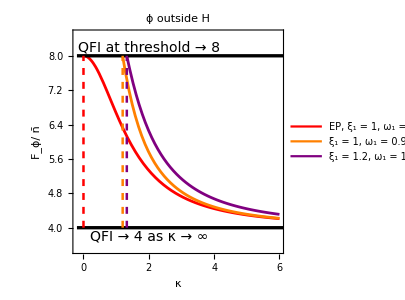

```mathematica
EP={Subscript[ξ, 1]->1,Subscript[ω, 1]->1};
aEP1={Subscript[ξ, 1]->1,Subscript[ω, 1]->0.8};
aEP2={Subscript[ξ, 1]->1.2,Subscript[ω, 1]->1};

th1=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1
th2=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2

max=6;
Show[Plot[{4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.EP},{κ,0,max},PlotRange->All,PlotStyle->Red, PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.9","ξ_1 = 1.2, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,.7}]],
Plot[4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.aEP1,{κ,th1,max},PlotStyle->Orange,PlotRange->{{-0.2,max},{4,8.5}}],
Plot[4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.aEP2,{κ,th2,max},PlotStyle->Purple,PlotRange->{{-0.2,max},{4,8.5}}],
Axes->None,PlotRange->{{-0.2,max},{3.5,8.5}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ϕ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,

Epilog->{Text[Style[TraditionalForm["QFI at threshold → 8"],14,Black,FontFamily->"Arial",Italic],{2,8.2}],Text[Style[TraditionalForm["QFI → 4 as κ → ∞"],14,Black,FontFamily->"Arial",Italic],{2,3.8}],Directive[Black,Thickness[0.008]],Line[{{-0.2,8},{max+0.2,8}}],Directive[Black,Thickness[0.008]],Line[{{-0.2,4},{max+0.2,4}}],Directive[Red,Thickness[0.006],Dashed],Line[{{0,4},{0,8}}],Directive[Orange,Thickness[0.006],Dashed],Line[{{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1,4},{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1,8}}],Directive[Purple,Thickness[0.006],Dashed],Line[{{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2,4},{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2,8}}]},PlotLabel->"ϕ outside H"
]
```

1.2

1.32665

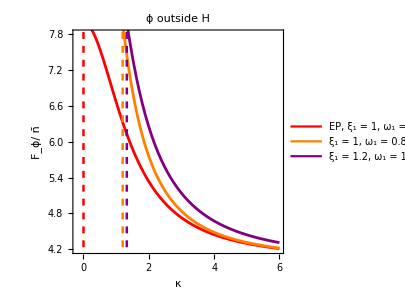

```mathematica
EP={Subscript[ξ, 1]->1,Subscript[ω, 1]->1};
aEP1={Subscript[ξ, 1]->1,Subscript[ω, 1]->0.8};
aEP2={Subscript[ξ, 1]->1.2,Subscript[ω, 1]->1};

th1=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1
th2=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2

max=6;
Show[Plot[{4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.EP},{κ,0,max},PlotRange->All,PlotStyle->Red, PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8","ξ_1 = 1.2, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,.7}]],
Plot[4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.aEP1,{κ,th1,max},PlotStyle->Orange,PlotRange->{{-0.2,max},{4,8.5}}],
Plot[4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.aEP2,{κ,th2,max},PlotStyle->Purple,PlotRange->{{-0.2,max},{4,8.5}}],
Axes->None,PlotRange->{{-0.2,max},{4.2,7.8}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ϕ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,

Epilog->{Directive[Red,Thickness[0.006],Dashed],Line[{{0,4},{0,8}}],Directive[Orange,Thickness[0.006],Dashed],Line[{{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1,4},{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1,8}}],Directive[Purple,Thickness[0.006],Dashed],Line[{{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2,4},{2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2,8}}]},PlotLabel->"ϕ outside H"
]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

Eigensystem at EP

{{-κ/2,-κ/2},{{-ⅈ,1},{0,0}}}

Eigensystem

{{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

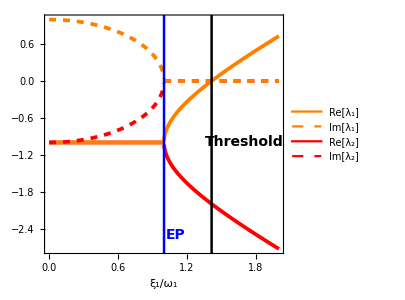

{{-1,-1},{{-ⅈ,1},{0,0}}}

{{-2,0},{{-(ⅈ √(1+ω_1^2))/(ⅈ+ω_1),1},{-(ⅈ √(1+ω_1^2))/(-ⅈ+ω_1),1}}}

√2

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"Eigensystem at EP"
Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]

"Eigensystem "
eig=Eigensystem[EOM]//FullSimplify

κ=2;
Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0,2},Axes->None,PlotStyle->{{Red,Thickness[0.009]},{Orange,Thickness[0.009]},{Red,Dashed,Thickness[0.009]},{Orange,Dashed,Thickness[0.009]}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["ξ_1/ω_1",18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Orange,{Orange,Dashed},Red,{Red,Dashed}},{"Re[λ_1]","Im[λ_1]","Re[λ_2]","Im[λ_2]"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}],Epilog->{Directive[Blue,Thickness[0.006]],Line[{{1,-3},{1,3}}],Text[Style["EP",14,Blue,FontFamily->"Arial",Bold],{1.1,-2.5}],Directive[Black,Thickness[0.006]],Line[{{Sqrt[2],-3},{Sqrt[2],3}}],Text[Style["Threshold",14,Black,FontFamily->"Arial",Bold],{1.7,-1}]}]

Eigensystem[EOM/.Subscript[ξ, 1]->1/.Subscript[ω, 1]->1]
Eigensystem[EOM/.Subscript[ξ, 1]->1/2 √(κ^2+4 Subscript[ω, 1]^2)]
1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1
```

```mathematica
Fn
```

4+(8 ξ_1^2)/(κ^2-2 ξ_1^2+4 ω_1^2)

```mathematica
κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2/.Subscript[ω, 1]->1/2 √(-κ^2+4 Subscript[ξ, 1]^2)
```

2 ξ_1^2

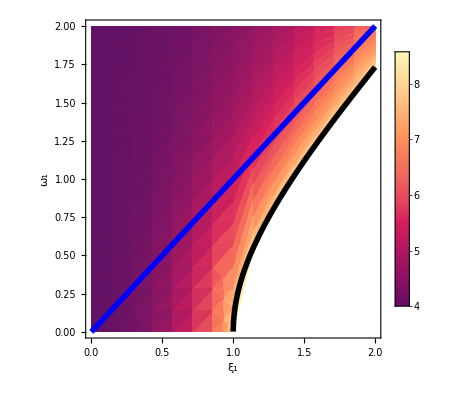

```mathematica
Show[DensityPlot[Fn/.{κ->2},{Subscript[ξ, 1],0,2},{Subscript[ω, 1],1/2 √(-κ^2+4 Subscript[ξ, 1]^2),2},PlotLegends->Automatic,FrameLabel->{"ξ_1","ω_1"},Exclusions->Automatic],Plot[1/2 √(-κ^2+4 Subscript[ξ, 1]^2)/.{κ->2},{Subscript[ξ, 1],0,2},AspectRatio->1,PlotRange->{0,2},PlotStyle->{Black,Thickness[0.01]}],Plot[Subscript[ξ, 1],{Subscript[ξ, 1],0,2},AspectRatio->1,PlotStyle->{Blue,Thickness[0.01]}]]
```

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]

(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];

Eigenvalues[EOM]
x1=0;p1=0;
{f,d,n}=QFIperPhotonBQH[Nmodes,EOM]
Assuming[{Subscript[ξ, 1],Subscript[ω, 1]}∈Reals&&Subscript[ξ, 1]>Subscript[ω, 1],f/n//FullSimplify]
Assuming[{Subscript[ξ, 1],Subscript[ω, 1]}∈Reals&&Subscript[ξ, 1]<Subscript[ω, 1],f/n//FullSimplify]


EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.Subscript[ω, 1]->Subscript[ξ, 1];
{f,d,n}=QFIperPhotonBQH[Nmodes,EOM]
Assuming[{Subscript[ξ, 1],Subscript[ω, 1]}∈Reals,f/n//FullSimplify]
```

{-√(ξ_1^2-ω_1^2),√(ξ_1^2-ω_1^2)}

{(8 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/((ξ_1^2-ω_1^2)^2),0,(Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2)/(ξ_1^2-ω_1^2)}

(8 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/(ξ_1^2-ω_1^2)

(8 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/(ξ_1^2-ω_1^2)

{8 (t^2 ξ_1^2+t^4 ξ_1^4),0,t^2 ξ_1^2}

8+8 t^2 ξ_1^2

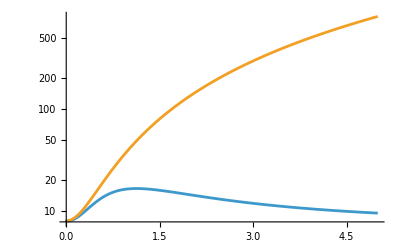

```mathematica
(* comparison loss with no loss *)
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=2;
Subscript[ω, 1]=2;
κ=1/2;

(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=5;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}];

S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes);

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);


plt1=LogPlot[{Evaluate[F/.ϕ->0]/n,8+8 t^2 Subscript[ξ, 1]^2},{t,0,tmax},PlotRange->All]
```

```mathematica
(* eq. 6.19-6.22 *)
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.

Ω={{0,1},{-1,0}};
Ω.Transpose[Ω]
"noise"
d=Sqrt[κ] IdentityMatrix[2];
c=Transpose[Ω].d;
"Loss in A"
(Ω.c.Ω.Transpose[c])/2//MatrixForm
"D matrix"
Ω.c.Transpose[c].Transpose[Ω]//MatrixForm
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

{{1,0},{0,1}}

noise

Loss in A

(-κ/2 | 0
0 | -κ/2)

D matrix

(κ | 0
0 | κ)

```mathematica
$Assumptions={Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
κ=1;
Subscript[ω, 1]->2;
Subscript[χ, 1,2]->1;
Nmodes=2;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[4]/.ZeroPhase[Nmodes]/.{Subscript[g, 1,2]->0,Subscript[ξ, 1]->0,Subscript[ξ, 2]->0,Subscript[ω, 2]->0};
EOM/.Subscript[ω, 1]->2 Subscript[χ, 1,2]//Eigensystem//FullSimplify
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

tmax=10;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}];
S=MatrixExp[DM t];
Σin=CovarBasis[Nmodes].(S.Transpose[S]+int).Transpose[CovarBasis[Nmodes]]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

{{-1/2-ⅈ χ_(1,2),-1/2-ⅈ χ_(1,2),-1/2+ⅈ χ_(1,2),-1/2+ⅈ χ_(1,2)},{{-ⅈ,0,0,1},{0,0,0,0},{0,-ⅈ,1,0},{0,0,0,0}}}

$Aborted

Thread::tdlen: Objects of unequal length in {{«1»},«3»}+{{73-ⅇ^(-t/2) (73+4 t Plus[«2»]),-64+8 ⅇ^(-t/2) (8+t Plus[«2»])},{-64+8 ⅇ^(-t/2) (8+t Plus[«2»]),57-ⅇ^(-t/2) (57+4 t Plus[«2»])}} cannot be combined.

```mathematica
CovarBasis[Nmodes]
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify;
"QFI limit"
Limit[F,t->∞]//N
"Mean photon limit"
Limit[n,t->∞]//N

plt1=Plot[{Evaluate[F/.ϕ->0]/n,8+8 t^2 Subscript[ξ, 1]^2},{t,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[LineLegend[{Blue,Purple,Red},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.3, ω_1 = 1","Threshold, ξ_1 = √2, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}]]
```